Logs
- [2025/12/23]   
  Use UndirectedEdge[“a”, “b”] to test it with MatchQ[]. 
 This code produces False instead of True
  MemberQ[{“a”<->”b”,”a”<->”d”,”a”<->”g”,”b”<->”c”,”b”<->”e”,”b”<->”f”},“a” <->”d”]

```mathematica
ClearAll["Global`*"]
```

```mathematica
l=Fibonacci[100]
```

354224848179261915075

```mathematica
m=2;
n=(m*l-1)/(m-1)
```

708449696358523830149

Find all possible spanning trees

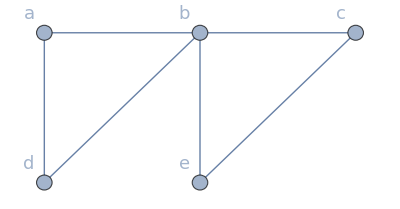

```mathematica
G1=Graph[{"a"<->"b","a"<->"d","b"<->"c","b"<->"d","b"<->"e","c"<->"e"},
VertexCoordinates->{"a"->{0,1},"b"->{1,1},"c"->{2,1},"d"->{0,0},"e"->{1,0}},
VertexSize->Small,EdgeStyle->Thick,VertexLabels->Placed["Name",{Before,Above}],VertexLabelStyle->Directive[FontSize->18,Italic]]
```

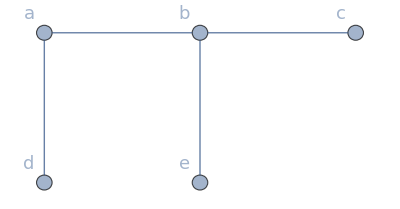
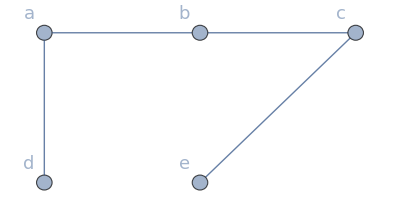
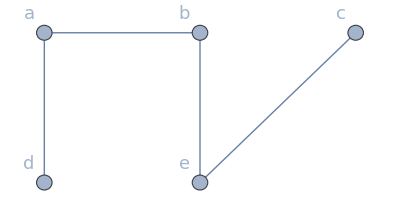
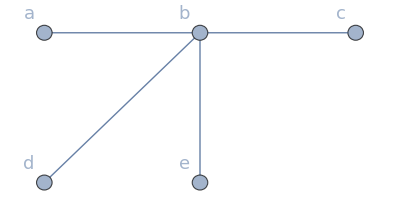
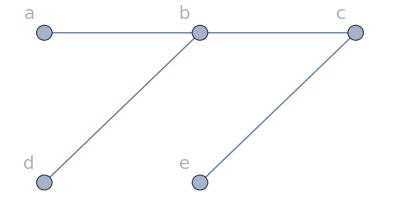
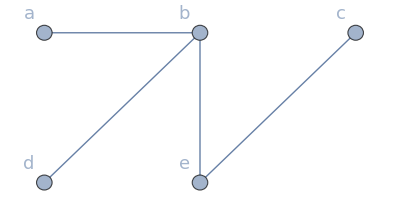
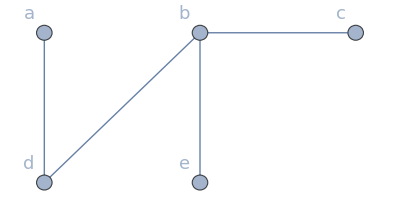
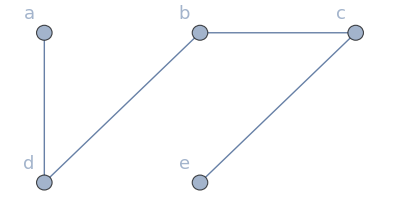

```mathematica
edges=EdgeList[G1];
nodesNum=VertexCount[G1];
getTrees=Select[
Subsets[edges,{nodesNum-1}],
ConnectedGraphQ[Graph[VertexList[G1],#]]&& AcyclicGraphQ[Graph[VertexList[G1],#]]&];
spanningTrees=Graph[VertexList[G1],#,VertexCoordinates->{"a"->{0,1},"b"->{1,1},"c"->{2,1},"d"->{0,0},"e"->{1,0}},
VertexSize->Small,EdgeStyle->Thick,VertexLabels->Placed["Name",{Before,Above}],VertexLabelStyle->Directive[FontSize->18,Italic]]&/@getTrees
```

```mathematica
Clear[curvyEdge];
curvyEdge[offset_?NumericQ]:=With[{off=offset},BezierCurve[{#1[[1]],{Mean[#1[[All,1]]],Max[#1[[All,2]]]+off},#1[[-1]]}]&];
G2=Graph[
{Labeled["d",Placed[{"d"},{{After, Below}}]],
Labeled["e",Placed[{"e"},{{After,Below}}]]},
{"a"<->"b","a"<->"d","a"<->"g","b"<->"c","b"<->"e","b"<->"f","b"<->"g","c"<->"d","c"<->"e","d"<->"e","d"<->"g","e"<->"f","e"<->"g","f"<->"g"},
VertexCoordinates->{"a"->{0,1},"b"->{1,1},"c"->{2,1},"d"->{3,0.5},"e"->{2,0},"f"->{1,0},"g"->{0,0}},
EdgeShapeFunction->{
"a"<->"d"->curvyEdge[1],
"g"<->"e"->curvyEdge[-1],
"d"<->"g"->curvyEdge[-2]},
VertexSize->Small,EdgeStyle->Thick,VertexLabels->Placed["Name",{Before,Above}],VertexLabelStyle->Directive[FontSize->18,Italic]];
ImageCrop[Rasterize[G2]]
```

-Graphics-

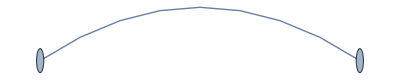

```mathematica
curvyEdge=(BezierCurve[{#1[[1]],{Mean[#1[[All,1]]],Max[#1[[All,2]]]+0.2},#1[[-1]]}]&);
Graph[{"a"<->"b"},EdgeShapeFunction->{"a"<->"b"->curvyEdge}]
```

```mathematica
Clear[curvyEdge];
edges=EdgeList[G2];
nodesNum=VertexCount[G2];
getTrees=Select[
Subsets[edges,{nodesNum-1}],
ConnectedGraphQ[Graph[VertexList[G2],#]]&& AcyclicGraphQ[Graph[VertexList[G2],#]]&];
numberToPrint=100;
Print["The number of possible spannig tree for G_2 is "<>ToString[Length[getTrees]]];
Print["We only print "<>ToString[numberToPrint]<>" spanning trees"];

curvyEdge[offset_?NumericQ]:=With[{off=offset},BezierCurve[{#1[[1]],{Mean[#1[[All,1]]],Max[#1[[All,2]]]+off},#1[[-1]]}]&];
spanningTreesG2=Table[Graph[{Labeled["d",Placed[{"d"},{{After, Below}}]],
Labeled["e",Placed[{"e"},{{After,Below}}]]},
tree,
VertexCoordinates->{
"a"->{0,1},"b"->{1,1},"c"->{2,1},"d"->{3,0.5},"e"->{2,0},"f"->{1,0},"g"->{0,0}},
VertexSize->Small,EdgeStyle->Thick,
EdgeShapeFunction->Select[{
UndirectedEdge["a","d"]->curvyEdge[1],
UndirectedEdge["g","e"]->curvyEdge[-1],
UndirectedEdge["d","g"]->curvyEdge[-2]},MemberQ[tree,First[#]]&],
VertexLabels->Placed["Name",{Before,Above}],
VertexLabelStyle->Directive[FontSize->18,Italic]],{tree,getTrees[[1;;100]]}];
gridOfGraphs=Grid[Partition[spanningTreesG2,UpTo[10]],Alignment->Center,Spacings->{1,1}]
Export[NotebookDirectory[]<>"spanning_trees_grid_"<>ToString[numberToPrint]<>".png",gridOfGraphs,ImageResolution->100]
```

The number of possible spannig tree for G_2 is 986

We only print 100 spanning trees

-Graphics-

/home/henokh/Documents/job-related/024 - SI ITK/ITK/Courses/SI-251-4009-discrete-mathematics-2/SI-251-4009-discrete-mathematics-2-github/programs/spanning_trees_grid_100.png

Debugging

```mathematica
"a"<->"d"->curvyEdge[1]
```

a<->d→(BezierCurve[{#1⟦1⟧,{Mean[#1⟦All,1⟧],Max[#1⟦All,2⟧]+1},#1⟦-1⟧}]&)

```mathematica
Table[tree,{tree,getTrees[[1;;10]]}]
```

{{a<->b,a<->d,a<->g,b<->c,b<->e,b<->f},{a<->b,a<->d,a<->g,b<->c,b<->e,e<->f},{a<->b,a<->d,a<->g,b<->c,b<->e,f<->g},{a<->b,a<->d,a<->g,b<->c,b<->f,c<->e},{a<->b,a<->d,a<->g,b<->c,b<->f,d<->e},{a<->b,a<->d,a<->g,b<->c,b<->f,e<->f},{a<->b,a<->d,a<->g,b<->c,b<->f,e<->g},{a<->b,a<->d,a<->g,b<->c,c<->e,e<->f},{a<->b,a<->d,a<->g,b<->c,c<->e,f<->g},{a<->b,a<->d,a<->g,b<->c,d<->e,e<->f}}

```mathematica
First["a"<->"d"->curvyEdge[1]]
```

a<->d

```mathematica
MemberQ[{"a" <-> "d"}, "a" <-> "d"]
```

True

```mathematica
Select[{"a"<->"d"->curvyEdge[1],"g"<->"e"->curvyEdge[-1],"d"<->"g"->curvyEdge[-2]},(True&)]
```

{a<->d→(BezierCurve[{#1⟦1⟧,{Mean[#1⟦All,1⟧],Max[#1⟦All,2⟧]+1},#1⟦-1⟧}]&),g<->e→(BezierCurve[{#1⟦1⟧,{Mean[#1⟦All,1⟧],Max[#1⟦All,2⟧]-1},#1⟦-1⟧}]&),d<->g→(BezierCurve[{#1⟦1⟧,{Mean[#1⟦All,1⟧],Max[#1⟦All,2⟧]-2},#1⟦-1⟧}]&)}

```mathematica
MemberQ[{"a"<->"b","a"<->"d","a"<->"g","b"<->"c","b"<->"e","b"<->"f"},UndirectedEdge["a","d"]]
```

True

```mathematica
Table[Select[{"a"<->"d"->curvyEdge[1],"g"<->"e"->curvyEdge[-1],"d"<->"g"->curvyEdge[-2]},MemberQ[tree,"a"<->"d"]&],{tree,getTrees[[1;;10]]}]
```

{{},{},{},{},{},{},{},{},{},{}}

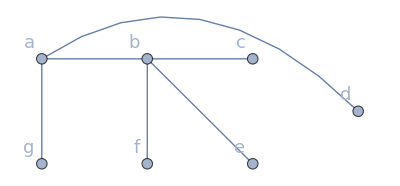

```mathematica
Graph[{"a"<->"b","a"<->"d","a"<->"g","b"<->"c","b"<->"e","b"<->"f"},VertexCoordinates->{"a"->{0,1},"b"->{1,1},"c"->{2,1},"d"->{3,0.5},"e"->{2,0},"f"->{1,0},"g"->{0,0}},VertexSize->Small,EdgeStyle->Thickness[Large],EdgeShapeFunction->{
"a"<->"d"->(BezierCurve[{#1⟦1⟧,{Mean[#1⟦All,1⟧],Max[#1⟦All,2⟧]+1},#1⟦-1⟧}]&)},
EdgeShapeFunction->Select[{"a"<->"d"->curvyEdge[1],"g"<->"e"->curvyEdge[-1],"d"<->"g"->curvyEdge[-2]},MemberQ[tree,First[#]]&],
VertexLabels->Placed["Name",{Before,Above}],VertexLabelStyle->Directive[FontSize->18,Italic]]
```

```mathematica
Length[spanningTreesG2]
```

986